```mathematica
SetDirectory[NotebookDirectory[]];
Re1=Import["./RedataT30mu320.dat"];
Im1=Import["./ImdataT30mu320.dat"];
p=Table[i*10,{i,0,200}];
spec=Transpose[{p,-1/π*Im1[[75]]/(Re1[[75]]^2+Im1[[75]]^2)}];
intRe=Table[Interpolation[Transpose[{p,Re1[[i]]}],InterpolationOrder->1],{i,1,201}];
intIm=Table[Interpolation[Transpose[{p,Im1[[i]]}],InterpolationOrder->1],{i,1,201}];
specList=Table[With[{fIm=intIm[[i]],fRe=intRe[[i]]},-(1/π)*fIm[#]/(fRe[#]^2+fIm[#]^2)&],{i,1,201} ];
```

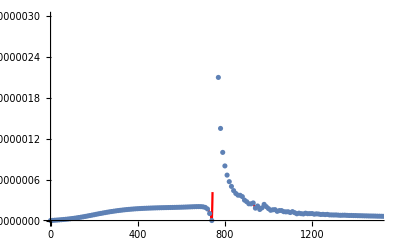

```mathematica
Show[Plot[specList[[75]][x],{x,0,2000},PlotPoints->30000,PlotStyle->Red],ListPlot[spec],PlotRange->{{0,1500},{-2 10^-8,3 10^-6}}]
```

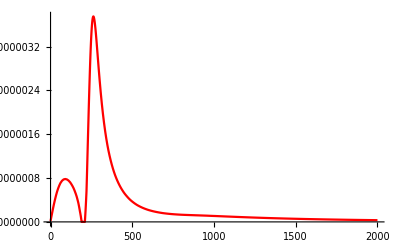

```mathematica
Plot[specList[[20]][x],{x,0,2000},PlotPoints->300,PlotStyle->Red,PlotRange->All]
```

```mathematica
specdata=Table[specList[[i]][x],{i,1,201},{x,1,2000,10}];
```

```mathematica
ListPlot3D[specdata(*,ScalingFunctions->Automatic*),PlotRange->{All,All,All}]
```

-Graphics3D-

```mathematica
specdata=Table[{1+(i-1)*10,spec[[j]][[i]]},{j,1,201},{i,1,Length[spec[[1]]]}];
```

```mathematica
Dimensions[specdata]
```

{201,201,2}

```mathematica
Table[Export["./rhodata/rho_data_p"<>ToString[(i-1)*10]<>".dat",specdata[[i]]],{i,1,201}];
```